```mathematica
(*
BaseDirectory is the location of the raw files. ScaledDirectory is where your files will be saved. 
You will have to change these to your directories.
You will have to create the folder "scaled" in this directory for the output files.
*)
BaseDirectory="C:\\Users\\maruk\\Desktop\\Research\\PHY242\\retake\\voltage\\raw";
ScaledDirectory="C:\\Users\\maruk\\Desktop\\Research\\PHY242\\retake\\voltage_scaled";
SetDirectory[BaseDirectory];
FileNames[]
```

{225R1.txt,225R2.txt,225R3.txt,225R4.txt,225R5.txt,225R6.txt,225R7.txt,250R1.txt,250R2.txt,250R3.txt,250R4.txt,250R5.txt,250R6.txt,250R7.txt,275R1.txt,275R2.txt,275R3.txt,275R4.txt,275R5.txt,275R6.txt,275R7.txt,300R1.txt,300R2.txt,300R3.txt,300R4.txt,300R5.txt,300R6.txt,300R7.txt,325R1.txt,325R2.txt,325R3.txt,325R4.txt,325R5.txt,325R6.txt,325R7.txt}

```mathematica
(*This is the module that we need to load.*)
process[in_,region_,out_]:=Module[{data,data2,save},
SetDirectory[BaseDirectory];
data=Import[in,"Table"];
data2=data;
data2[[All,1]]=-4 data[[All,1]]+3200+2 640(region-3);
data2[[All,2]]=4 data[[All,2]];
Print[GraphicsRow[{ListPlot[data[[All,{1,3}]],PlotLabel->"Before Processing",PlotRange->All],ListPlot[data2[[All,{1,3}]],PlotLabel->"After Processing",PlotRange->All]}]];
save=ChoiceDialog["Save processed data?",{"Save"->True,"Don't Save"->False}];
If[save,SetDirectory[ScaledDirectory];Export[out,data2,"Table"]];
]
```

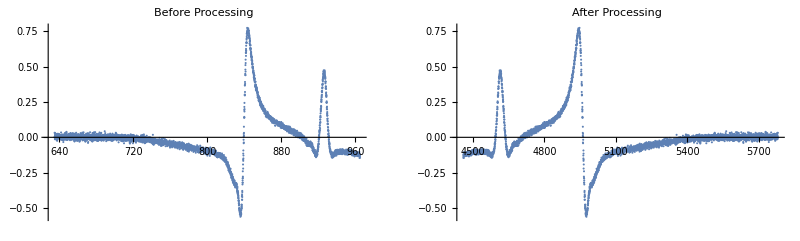

```mathematica
process["225R7.txt",7,"225R1scaled.txt"]
```

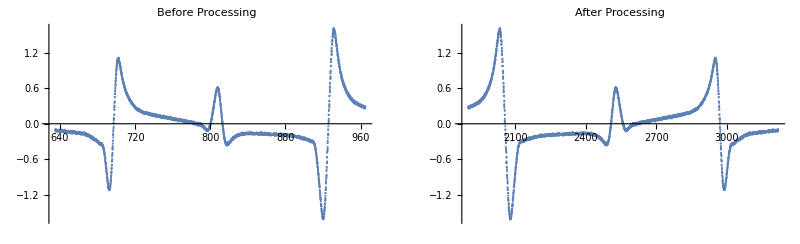

```mathematica
process["225R6.txt",5,"225R5scaled.txt"]
```

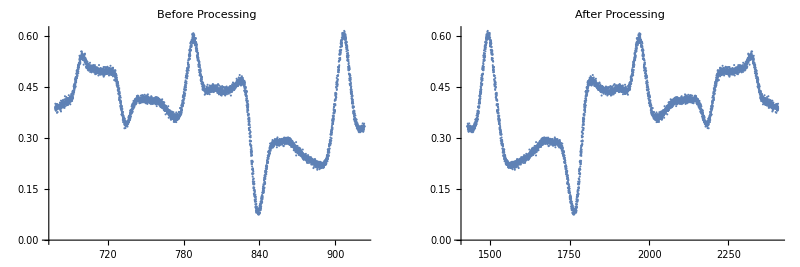

```mathematica
process["trial03.txt",5,"trial03scaled.txt"]
```

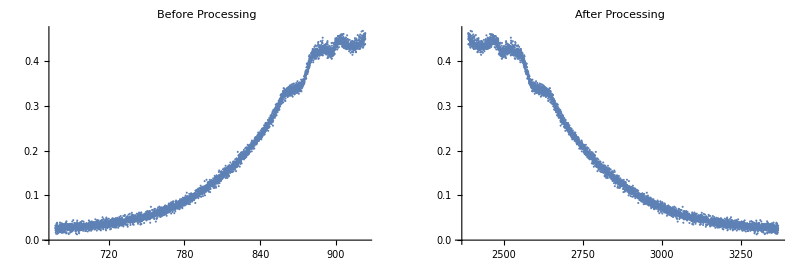

```mathematica
process["trial04.txt",6,"trial04scaled.txt"]
```

```mathematica
file =StringJoin[ToString[225],"R", ToString[1],".txt"]
```

225R1.txt

```mathematica
namingConvention[voltage_,region_]:=Module[{name,names,scaled},
name = StringJoin[ToString[voltage],"R", ToString[region],".txt"];
scaled = StringJoin[ToString[voltage],"R", ToString[region],"scaled",".txt"];
names = {name,scaled};
Return[names]]
```

```mathematica
massProcess[val_]:=Module[{data,data2,save,i,in,out,region},
For[i=1,i≤7,i++,
SetDirectory[BaseDirectory];
region=i;
{in,out}=namingConvention[val,i];
data=Import[in,"Table"];
data2=data;
data2[[All,1]]=-4 data[[All,1]]+3200+2 640(region-3);
data2[[All,2]]=4 data[[All,2]];
SetDirectory[ScaledDirectory];Export[out,data2,"Table"]];
]
```

```mathematica
massProcess[225]
```

```mathematica
For[j=250,j≤325,j+=25,
massProcess[j]]
```

```mathematica
massProcess[225]
```